```mathematica
(*Find B_stable that meets G(a)=0,G'(a)<0 and 0<n<1*)
```

```mathematica
γ=4.81;δ=0.0289;m=2;α=0.0395;β=0.6;βc=0.0451;ka=1.316;kb=0.045;pr=1.77;pc=1.23;n1=2;n2=1;i=1;(*Fix I_n=1, i=1*)
W=Table[NSolve[{γ*n-δ*a==0,((α+β)*((ka*a+1)^n1+(pr/δ)^n1)/((ka*a+1)^n1*(kb*b+1)+(pr/δ)^n1)-β-βc*(i*(pc/δ)^n2)/(i*(pc/δ)^n2+(ka*a+1)^n2))*n*(1-n^m)==0,y==b},{a,n,y}],{b,0,5,0.02}];(*The initial range of B_n is given as (0,5)*)
s1={y,n}/.W;
```

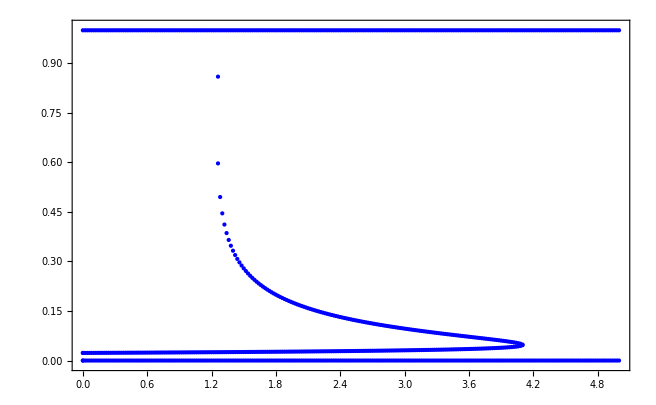

```mathematica
a1=ListPlot[s1,PlotStyle->RGBColor[0,0,1],AxesOrigin->{0,0},BaseStyle->{FontWeight->"Bold",FontSize->8},PlotRange->{{0,5},{-0.01,1.01}},Frame->True]
```

```mathematica
(*Find B_stable is (1.26,4.1)*)
```

```mathematica
(*Calculate tau0 by iteratively taking the value b in B_stable at step 0.1 (or 0.01) and find the b that satisfies tau0>72,thus determining B_robust*)
```

```mathematica
(*Kernel needs to be exited before calculating*)
γ=4.81;δ=0.0289;m=2;α=0.0395;β=0.6;βc=0.0451;ka=1.316;kb=0.045;pr=1.77;pc=1.23;n1=2;n2=1;i=1;
b=1.3;(*iteratively taking the value b in B_stable*)
NSolve[{γ*n-δ*a==0,((α+β)*((ka*a+1)^n1+(pr/δ)^n1)/((ka*a+1)^n1*(kb*b+1)+(pr/δ)^n1)-β-βc*(i*(pc/δ)^n2)/(i*(pc/δ)^n2+(ka*a+1)^n2))==0},{a,n}]
```

{{a→237.869,n→1.42919},{a→74.1703,n→0.445639},{a→4.22604,n→0.0253914}}

```mathematica
Ga=((α+β)*((ka*a+1)^n1+(pr/δ)^n1)/((ka*a+1)^n1*(kb*b+1)+(pr/δ)^n1)-β-βc*(i*(pc/δ)^n2)/(i*(pc/δ)^n2+(ka*a+1)^n2))；
```

```mathematica
Ga1=D[Ga,a];
```

```mathematica
a=74.1703052152631;n=0.4456386321665496;(*Find {E^*} using Ga1<0*)
f1=-(b ka (1+a ka)^(-1+n1) kb n1 (α+β) (pr/δ)^n1)/(((1+a ka)^n1 (1+b kb)+(pr/δ)^n1)^2);
g1=-(i ka (1+a ka)^(-1+n2) n2 βc (pc/δ)^n2)/(((1+a ka)^n2+i (pc/δ)^n2)^2);
F=n(1-n^m);
NSolve[-F^2 f1^2 γ^2+F^2 g1^2 γ^2+(-2 F g1 γ+δ^2) ω^2+ω^4==0,ω](*Calculate ω and select the value of ω>0*)
```

{{ω→-0.00637108},{ω→0.-0.0362117 ⅈ},{ω→0.+0.0362117 ⅈ},{ω→0.00637108}}

```mathematica
ω=0.006371075084319424;(*Substitute ω to calculate tau0*)
tau0=ArcCos[(F g1 γ-ω^2)/(F f1 γ)]/ω
```

97.193

```mathematica
(*By iteratively taking the value b,we can calculate B_robust=(1.26,1.37)U(3.3,4.1). By choosing b=1.3,we can calculate E_l^*=(4.23,0.025)*)
```